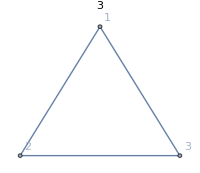
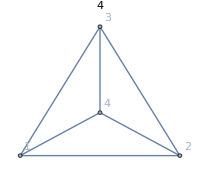
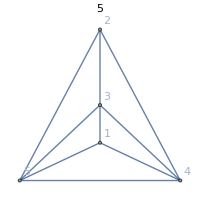
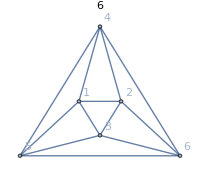
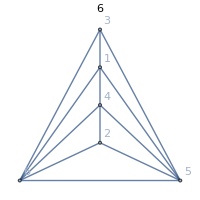
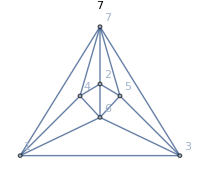
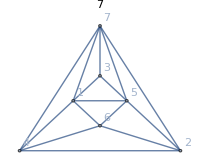
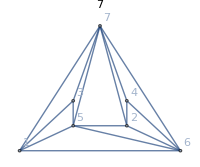

```mathematica
Table[Show[Graph[GraphData[k],GraphLayout->"TutteEmbedding", VertexLabels->"Name", PlotLabel->Style[VertexCount[GraphData[k]],Bold,FontSize->20, Red, Background->Lighter[Yellow]]],ImageSize->200],{k,Sort[GraphData["Triangulated"],VertexCount[GraphData[#1]]<VertexCount[GraphData[#2]]&]}]
```